```mathematica
Clear["Global`*"];
```

```mathematica
booster=Delete[Import["Data.xlsx", Path->NotebookDirectory[]][[3]], 1];
```

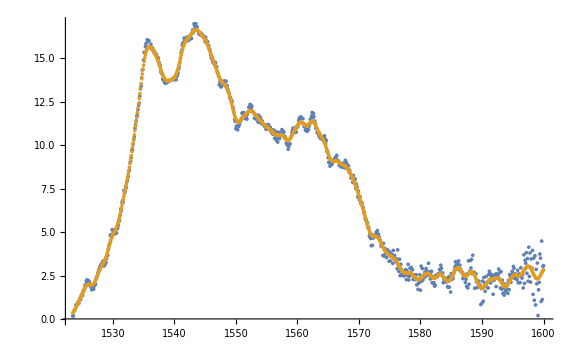

```mathematica
ListPlot[{
booster,
Parallelize[Table[{booster[[i,1]],GaussianFilter[booster[[All,2]],Filter=10][[i]]}, {i,1, Length[booster]}]]
}, ImageSize->Large, PlotLegends->"GaussianFilter"]
```

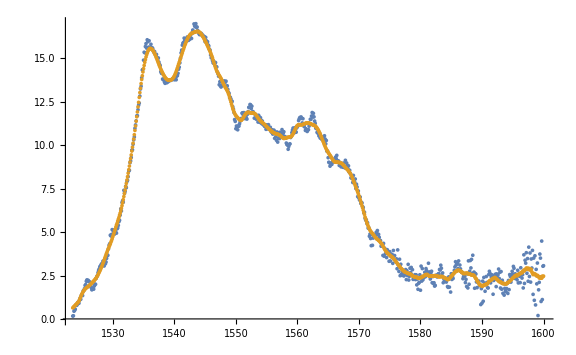

```mathematica
ListPlot[{
booster,
Parallelize[Table[{booster[[i,1]],MeanFilter[booster[[All,2]],Filter=10][[i]]}, {i,1, Length[booster]}]]
}, ImageSize->Large, PlotLegends->"MeanFilter"]
```

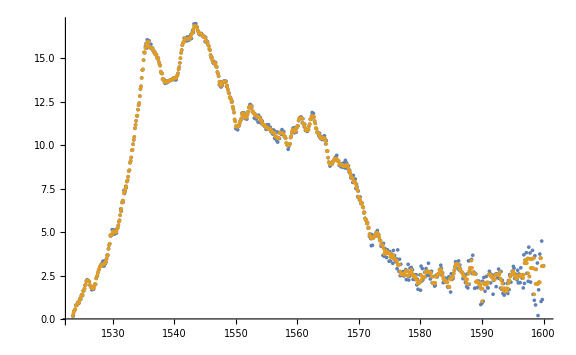

```mathematica
ListPlot[{
booster,
Parallelize[Table[{booster[[i,1]],MedianFilter[booster[[All,2]],Filter=2][[i]]}, {i,1, Length[booster]}]]
}, ImageSize->Large, PlotLegends->"MedianFilter"]
```

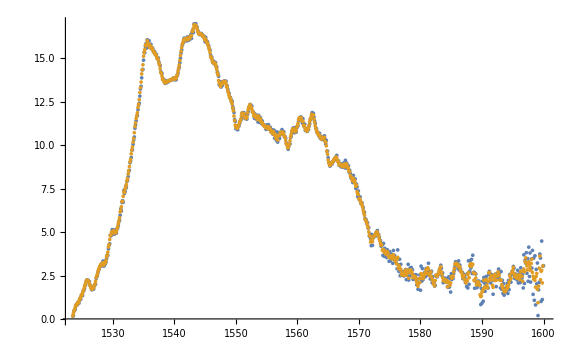

```mathematica
ListPlot[{
booster,
Parallelize[Table[{booster[[i,1]],MovingAverage[booster[[All,2]],Filter=2][[i]]}, {i,1, Length[booster]}]]
}, ImageSize->Large, PlotLegends->"MovingAverage"]
```

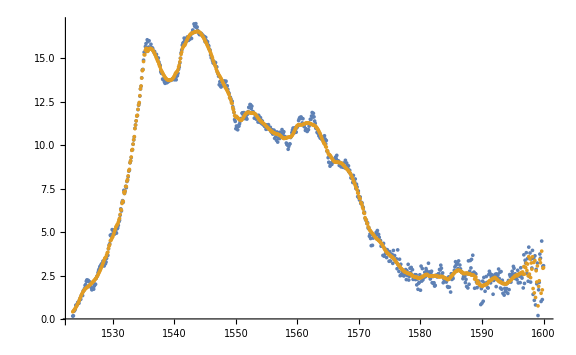

```mathematica
ListPlot[{
booster,
Parallelize[Table[{booster[[i,1]],WienerFilter[booster[[All,2]],Filter=10][[i]]}, {i,1, Length[booster]}]]
}, ImageSize->Large, PlotLegends->"WienerFilter"]
```

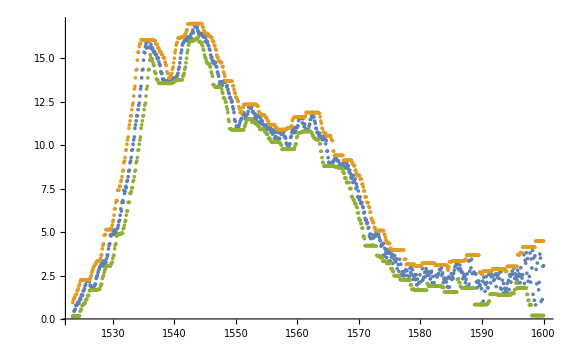

```mathematica
ListPlot[{
booster,
Parallelize[Table[{booster[[i,1]],MaxFilter[booster[[All,2]],Filter=10][[i]]}, {i,1, Length[booster]}]],
Parallelize[Table[{booster[[i,1]],MinFilter[booster[[All,2]],Filter=10][[i]]}, {i,1, Length[booster]}]]
}, ImageSize->Large, PlotLegends->"Max/Min Filter"]
```

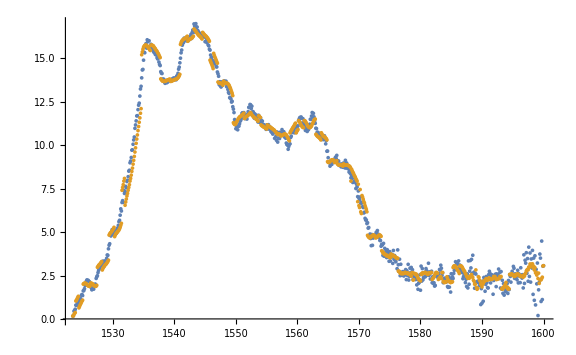

```mathematica
ListPlot[{
booster,
Parallelize[Table[{booster[[i,1]],KuwaharaFilter[booster[[All,2]],Filter=10][[i]]}, {i,1, Length[booster]}]]
}, ImageSize->Large, PlotLegends->"KuwaharaFilter"]
```